```mathematica
n=3;ep=LeviCivitaTensor[3,List];alcoord={al,be,ga};alcoordd={aldot,bedot,gadot};phcoord={phx,phy,phz};phcoordd={phxdot,phydot,phzdot};phpcoord={phpx,phpy,phpz};phpcoordd={phpxdot,phpydot,phpzdot};gap={gapx,gapy,gapz};reuler={{Cos[al] Cos[ga]-Cos[be] Sin[al] Sin[ga],Cos[ga] Sin[al]+Cos[al] Cos[be] Sin[ga],Sin[be] Sin[ga]},{-Cos[be] Cos[ga] Sin[al]-Cos[al] Sin[ga],Cos[al] Cos[be] Cos[ga]-Sin[al] Sin[ga],Cos[ga] Sin[be]},{Sin[al] Sin[be],-Cos[al] Sin[be],Cos[be]}};inversereuler=Simplify[Inverse[reuler]];MatrixForm[inversereuler]
```

(Cos[al] Cos[ga]-Cos[be] Sin[al] Sin[ga] | -Cos[be] Cos[ga] Sin[al]-Cos[al] Sin[ga] | Sin[al] Sin[be]
Cos[ga] Sin[al]+Cos[al] Cos[be] Sin[ga] | Cos[al] Cos[be] Cos[ga]-Sin[al] Sin[ga] | -Cos[al] Sin[be]
Sin[be] Sin[ga] | Cos[ga] Sin[be] | Cos[be])

```mathematica
(* angular velocity *)
```

```mathematica
tranalphp={{Sin[be]*Sin[ga],Cos[ga],0},{Sin[be]*Cos[ga],-Sin[ga],0},{Cos[be],0,1}};inversetranalphp=Simplify[Inverse[tranalphp]];omp=tranalphp.alcoordd;omi=Simplify[inversereuler.omp,Assumptions->{al∈Reals,be∈Reals,ga∈Reals}];ompf=omp/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};omif=omi/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};xpaxis={Cos[al]*Cos[ga]-Sin[al]*Cos[be]*Sin[ga],Sin[al]*Cos[ga]+Cos[al]*Cos[be]*Sin[ga],Sin[be]*Sin[ga]};ypaxis={-Cos[al]*Sin[ga]-Sin[al]*Cos[be]*Cos[ga],-Sin[al]*Sin[ga]+Cos[al]*Cos[be]*Cos[ga],Sin[be]*Cos[ga]};zpaxis={Sin[be]*Sin[al],-Sin[be]*Cos[al],Cos[be]};xpaxisf=xpaxis/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};ypaxisf=ypaxis/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};zpaxisf=zpaxis/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};
```

```mathematica
(* kinetic energy and angular momentum *)
```

```mathematica
ip={{ipxx,0,0},{0,ipyy,0},{0,0,ipzz}};tp=Simplify[1/2*Sum[ip[[i,j]]*omp[[i]]*omp[[j]],{i,1,n},{j,1,n}]];lp=ip.omp;li=Simplify[inversereuler.lp,Assumptions->{al∈Reals,be∈Reals,ga∈Reals}];MatrixForm[li]
```

(ipzz (gadot+aldot Cos[be]) Sin[al] Sin[be]-ipyy (aldot Cos[ga] Sin[be]-bedot Sin[ga]) (Cos[be] Cos[ga] Sin[al]+Cos[al] Sin[ga])+ipxx (Cos[al] Cos[ga]-Cos[be] Sin[al] Sin[ga]) (bedot Cos[ga]+aldot Sin[be] Sin[ga])
-ipzz Cos[al] (gadot+aldot Cos[be]) Sin[be]+ipyy (aldot Cos[ga] Sin[be]-bedot Sin[ga]) (Cos[al] Cos[be] Cos[ga]-Sin[al] Sin[ga])+ipxx (Cos[ga] Sin[al]+Cos[al] Cos[be] Sin[ga]) (bedot Cos[ga]+aldot Sin[be] Sin[ga])
gadot ipzz Cos[be]+aldot ipzz Cos[be]^2+Sin[be] (aldot ipyy Cos[ga]^2 Sin[be]+bedot (ipxx-ipyy) Cos[ga] Sin[ga]+aldot ipxx Sin[be] Sin[ga]^2))

```mathematica
(* potential energy *)
```

```mathematica
scoeffi={{sxx,sxy,sxz},{sxy,syy,syz},{sxz,syz,szz}};scoeffp=Table[Simplify[Sum[reuler[[k,i]]*reuler[[l,j]]*scoeffi[[i,j]],{i,1,n},{j,1,n}]],{k,1,n},{l,1,n}];deeg=cc*scoeffp[[3,3]];
```

```mathematica
(* Euler equation *)
```

```mathematica
gaplv=Table[Simplify[Sum[-2*cc*scoeffi[[j,k]]*reuler[[3,k]]*inversereuler[[j,l]]*ep[[i,3,l]],{j,1,n},{k,1,n},{l,1,n}]],{i,1,n}];eueq1=Table[Simplify[D[Sum[ip[[i,j]]*ompf[[j]],{j,1,n}],t]+Sum[ip[[j,k]]*omp[[j]]*omp[[l]]*ep[[l,k,i]],{j,1,n},{k,1,n},{l,1,n}]-gaplv[[i]]/.{al->alf[t],be->bef[t],ga->gaf[t]}],{i,1,n}]/.{alf''[t]->alddot,bef''[t]->beddot,gaf''[t]->gaddot,alf'[t]->aldot,bef'[t]->bedot,gaf'[t]->gadot,alf[t]->al,bef[t]->be,gaf[t]->ga};eueq2=Table[Simplify[Sum[eueq1[[i]]*tranalphp[[i,j]],{i,1,n}]],{j,1,n}];gaallv=Table[Simplify[-D[deeg,alcoord[[i]]]],{i,1,n}];eueq4=Table[Simplify[D[D[tp,alcoordd[[i]]]/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]},t]-D[tp,alcoord[[i]]]-gaallv[[i]]/.{alf''[t]->alddot,bef''[t]->beddot,gaf''[t]->gaddot,alf'[t]->aldot,bef'[t]->bedot,gaf'[t]->gadot,alf[t]->al,bef[t]->be,gaf[t]->ga}],{i,1,n}];Simplify[eueq2-eueq4]
```

{0,0,0}

```mathematica
(* m̂ *)
```

```mathematica
mhatp={Sin[ch]*Cos[la],Sin[ch]*Sin[la],Cos[ch]};mhati=Simplify[inversereuler.mhatp];MatrixForm[mhati]
```

(Cos[ch] Sin[al] Sin[be]+Sin[ch] (Cos[al] Cos[ga+la]-Cos[be] Sin[al] Sin[ga+la])
Cos[ga+la] Sin[al] Sin[ch]+Cos[al] (-Cos[ch] Sin[be]+Cos[be] Sin[ch] Sin[ga+la])
Cos[be] Cos[ch]+Sin[be] Sin[ch] Sin[ga+la])

```mathematica
nhati={Sin[tho]*Cos[pho],Sin[tho]*Sin[pho],Cos[tho]};mdotn=Simplify[mhati.nhati]
```

Cos[tho] Sin[be] Sin[ch] Sin[ga+la]+(Cos[ga+la] Cos[al-pho] Sin[ch]+Cos[ch] Sin[be] Sin[al-pho]) Sin[tho]+Cos[be] (Cos[ch] Cos[tho]-Sin[ch] Sin[ga+la] Sin[al-pho] Sin[tho])

```mathematica
(* analytical cone model *)
```

```mathematica
ief=aldot+gadot*(Cos[be]-Sin[ga+la]*Sin[be]*Cot[ch])/((Sin[be]*Cot[ch]-Cos[be]*Sin[ga+la])^2+(Cos[ga+la])^2);wid=2*ArcCos[(Cos[rh]-mhati[[3]]*Cos[tho])/(Sqrt[1-(mhati[[3]])^2]*Sin[tho])];
```

```mathematica
(* numerical approach *)
```

```mathematica
cc1=1;cc2=0;sxx1=-0.01;syy1=0.02;szz1=0.05;sxy1=0.0;sxz1=0.0;syz1=0;ipxx1=1;ipyy1=1;ipzz1=1.1;tf1=1600;numeueq=eueq4/.{cc->cc1,sxx->sxx1,syy->syy1,szz->szz1,sxy->sxy1,sxz->sxz1,syz->syz1,ipxx->ipxx1,ipyy->ipyy1,ipzz->ipzz1,al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t],alddot->alf''[t],beddot->bef''[t],gaddot->gaf''[t]};numeueq2=eueq4/.{cc->cc2,sxx->sxx1,syy->syy1,szz->szz1,sxy->sxy1,sxz->sxz1,syz->syz1,ipxx->ipxx1,ipyy->ipyy1,ipzz->ipzz1,al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t],alddot->alf''[t],beddot->bef''[t],gaddot->gaf''[t]};tho2=0.8;pho2=0;ch2=0.5;la2=0;rh2=0.6;mdotn1=mdotn/.{tho->tho2,pho->pho2,ch->ch2,la->la2,al->alf[t],be->bef[t],ga->gaf[t]};ief1=ief/.{rh->rh2,tho->tho2,pho->pho2,ch->ch2,la->la2,al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};wid1=wid/.{rh->rh2,tho->tho2,pho->pho2,ch->ch2,la->la2,al->alf[t],be->bef[t],ga->gaf[t]};
```

```mathematica
(* solution I *)
```

```mathematica
al1=Pi/2;be1=0.697;ga1=0;aldot1=1.391;bedot1=0;gadot1=1-aldot1*Cos[be1];solal=NDSolve[{numeueq[[1]]==0,numeueq[[2]]==0,numeueq[[3]]==0,alf[0]==al1,bef[0]==be1,gaf[0]==ga1,alf'[0]==aldot1,bef'[0]==bedot1,gaf'[0]==gadot1},{alf,bef,gaf},{t,0,tf1}]
```

{{alf→InterpolatingFunction[{{0., 800.}}, <>],bef→InterpolatingFunction[{{0., 800.}}, <>],gaf→InterpolatingFunction[{{0., 800.}}, <>]}}

```mathematica
(* solution II *)
```

```mathematica
al1=Pi/2;be1=1.060;ga1=0;aldot1=0.770;bedot1=0;gadot1=1-aldot1*Cos[be1];solal=NDSolve[{numeueq[[1]]==0,numeueq[[2]]==0,numeueq[[3]]==0,alf[0]==al1,bef[0]==be1,gaf[0]==ga1,alf'[0]==aldot1,bef'[0]==bedot1,gaf'[0]==gadot1},{alf,bef,gaf},{t,0,tf1}]
```

{{alf→InterpolatingFunction[{{0., 1600.}}, <>],bef→InterpolatingFunction[{{0., 1600.}}, <>],gaf→InterpolatingFunction[{{0., 1600.}}, <>]}}

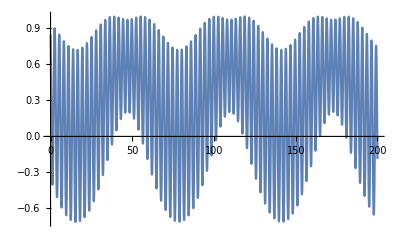

```mathematica
function=Evaluate[mdotn1/.solal[[1]]];Plot[function,{t,0,200},PlotRange->All]
```